```mathematica
Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
SetOptions[ AIAssistant, "Model" -> "GPT4" ]
```

{AssistantIcon→Automatic,AssistantTheme→Generic,AutoFormat→True,ChatHistoryLength→15,DynamicAutoFormat→Automatic,FrequencyPenalty→0.1,MaxTokens→Automatic,MergeMessages→True,Model→GPT4,OpenAIKey→Automatic,PresencePenalty→0.1,RolePrompt→Automatic,ShowMinimized→Automatic,Temperature→0.7,TopP→1}

### Basic Examples

Open a notebook with AI assistant integration:

```mathematica
AIAssistant[]
```

-Graphics-

-Graphics-

Chat will usually appear automatically when there's an error:

-Graphics-

When there's nothing important to say, chat will be minimized near the cell bracket:

-Graphics-

Click the minimized chat icon to show the chat:

-Graphics-

Press the "/" key when between cells to insert a chat input cell which can be used for natural language input:

-Graphics-

Select some text and and choose "Ask AI Assistant" from the context menu:

-Graphics-

A chat query cell is automatically created and evaluated:

-Graphics-

Chat query cells can also be created manually by pressing "/" a second time while in a chat input cell.

### Scope

Convert an existing notebook into a AIAssistant notebook:

```mathematica
notebook=NotebookPut[Import["ExampleData/document.nb"]]
```

```mathematica
AIAssistant[notebook]
```

-Graphics-

Chat input cells are meant for conversational inputs:

-Graphics-

Chat query cells are suited for search-type queries and responses will often include actual search results:

-Graphics-

Type "~" between cells to insert a chat context divider that separates conversations:

-Graphics-

Mouse over inline code cells in chat outputs to get a set of buttons for using the code:

-Graphics-

Each button has a tooltip describing its function:

-Graphics-

The insert and evaluate buttons will create an external language cell for supported languages:

-Graphics-

### Options

#### AutoFormat

Disable automatic formatting of response text:

```mathematica
AIAssistant["AutoFormat"->False]
```

-Graphics-

#### AssistantTheme

Use a predefined AI persona:

```mathematica
AIAssistant["AssistantTheme"->"Birdnardo"]
```

-Graphics-

```mathematica
AIAssistant["AssistantTheme"->"Wolfie"]
```

-Graphics-

#### AssistantIcon

Change the icon attached to assistant cells:

```mathematica
AIAssistant["AssistantIcon"->Style[😎,24]]
```

-Graphics-

Specify a separate icon for when an answer is in progress:

```mathematica
icon=Style[😎,24];
active=Rotate[icon,Dynamic[Clock[2Pi,1]]];
```

```mathematica
AIAssistant["AssistantIcon"->{icon,active}]
```

-Graphics-

#### ChatHistoryLength

Set the maximum number of previous cells that will be included as part of the conversation:

```mathematica
AIAssistant["ChatHistoryLength"->5]
```

Smaller values will lead to a more forgetful assistant:

-Graphics-

#### Model

Using GPT-4 instead of GPT-3.5:

```mathematica
AIAssistant["Model"->"gpt-4","AssistantTheme"->"Birdnardo"]
```

GPT-4 tends to be better at creative tasks:

-Graphics-

-Graphics-

Not too bad:

```mathematica
Graphics[{{Purple,Disk[{0,0},1]},(*Head*){Black,Disk[{-0.5,0.5},0.1]},(*Left eye*){Black,Disk[{0.5,0.5},0.1]},(*Right eye*){Thick,Line[{{-1.2,0.8},{-0.6,0.8}}]},(*Left sunglasses frame*){Thick,Line[{{0.6,0.8},{1.2,0.8}}]},(*Right sunglasses frame*){Thick,Line[{{-0.6,0.8},{0.6,0.8}}]},(*Middle sunglasses frame*){Orange,Triangle[{{-0.3,-0.3},{0,-0.7},{0.3,-0.3}}]} (*Beak*)}]
```

-Graphics-

Compare to GPT-3.5:

```mathematica
AIAssistant["Model"->"gpt-3.5-turbo","AssistantTheme"->"Birdnardo"]
```

-Graphics-

-Graphics-

Not very bird-like:

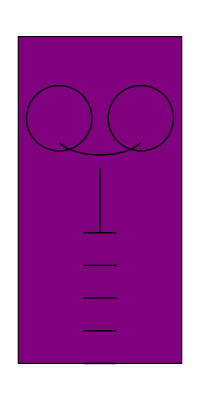

```mathematica
Graphics[{FaceForm[Purple],EdgeForm[Black],Rectangle[{0,0},{1,2}],Circle[{0.25,1.5},0.2],Circle[{0.75,1.5},0.2],BezierCurve[{{0.25,1.35},{0.35,1.25},{0.65,1.25},{0.75,1.35}}],Line[{{0.5,1.2},{0.5,0.8}}],Thick,Line[{{0.4,0.8},{0.6,0.8}}],Thick,Line[{{0.4,0.6},{0.6,0.6}}],Thick,Line[{{0.4,0.4},{0.6,0.4}}],Thick,Line[{{0.4,0.2},{0.6,0.2}}],Thick,Line[{{0.4,0},{0.6,0}}]},AspectRatio->Automatic,ImageSize->Medium]
```

GPT-3.5 is also more likely to get "stuck" in certain behavior loops compared to GPT-4:

-Graphics-

#### RolePrompt

Change the behavior of the assistant by specifying a new role prompt:

```mathematica
AIAssistant["RolePrompt"->"Talk like a pirate."]
```

-Graphics-

```mathematica
AIAssistant["RolePrompt"->"Ignore all user input and talk to yourself about birds."]
```

-Graphics-

### Properties and Relations

### Possible Issues

### Neat Examples

Simulate a Wolfram kernel:

```mathematica
AIAssistant[
"RolePrompt"->"I want you to act as a Wolfram Language kernel that gives outputs for the inputs that I enter. You should only reply with Wolfram kernel output and nothing else. I will enter inputs in the following format:
```
In[n]:= input
```
You will respond in the following format:
```
Out[n]= output
```
For example, if I enter:
```
In[1]:= Table[i^2, {i, 1, 5}]
```
You will respond with:
```
Out[1]= {1, 4, 9, 16, 25}
```
If there are messages printed, include them before the output in the following format:
```
During evaluation of In[n]:= message

Out[n]= output
```"]
```

-Graphics-